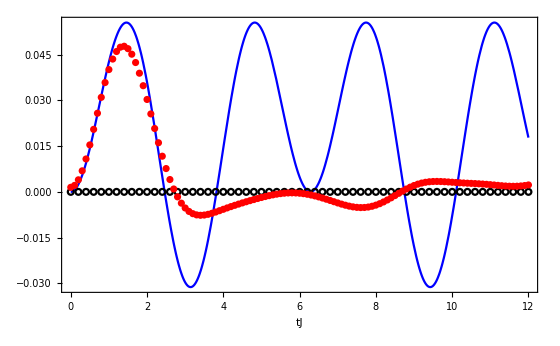

```mathematica
Legended[Show[%386,%556,%536,FrameLabel->Style["tJ",Italic,28],Frame->True,ImageSize->560,PlotRange->All,LabelStyle->Directive[FontSize->20,Black,FontFamily->"Times New Roman"]],Placed[SwatchLegend[{Blue, Black, Red},{Style["Exact",18],Style["dTWA",18],Style["TWA",18]},LabelStyle->(FontFamily->"Arial"),LegendFunction->Panel,Alignment->Center,LegendMarkers->{Graphics[{Thick,Line[{{0,0},{1,0}}]}],Graphics[Circle[],ImageSize->5],"Bubble"}],{0.1,0.17}]]
```

# Exact

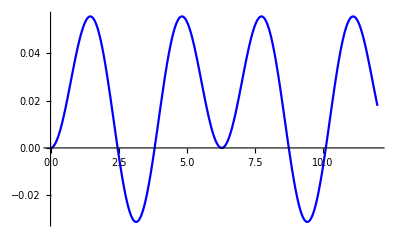

```mathematica
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/4;(*Polar Angle*)
alpha =3;
num=20;
(*NOTE: ALL THE LATTICES WILL HAVE EDGE EFFECTS*)

(*creates the linear lattice*)
list:=Table[i,{i,num}];
(*where 11 is number of particles and can be changed*)
(*i=list⟦5⟧;(*First particle of the triple*)
j=list⟦6⟧;(*Second particle of the triple*)*)





(*Define Interactions & Bloch Vector*)(*everything in terms of S, not sigma*)
(*1 is x, -1 is y, 0 is z*)
(*add d, etc. for additional spins*)
cutoff[epsilon_]:=If[Abs[epsilon] > 10^-8,epsilon,0];
hoSVD[m_]:=N[With[{d=ArrayDepth[m]},{Fold[Transpose[#1,RotateRight@Range[d]].#2&,m,#],ConjugateTranspose/@#}&@Table[Conjugate@First@SingularValueDecomposition@Flatten[m,{{i},Delete[Range[d],i]}],{i,d}]]];
J[i_,j_]:=(*If[i-j==0,0,jstrength/Abs[i-j]^alpha]; *)If[Abs[i-j]==1,jstrength,0](*1/Abs[j-i]^3*); (*Interaction function J depends on experimental scenario, these are two examples*)
gp[x_,θ_]:=N[Cos[θ/2]^2 ⅇ^(-ⅈ x/2)+Sin[θ/2]^2 ⅇ^(ⅈ x/2)]; 
gm[x_,θ_]:=N[Cos[θ/2]^2 ⅇ^(-ⅈ x/2)-Sin[θ/2]^2 ⅇ^(ⅈ x/2)(*+10^-20*)];(*10^-20 is to prevent 0^0 at theta = pi/2,but has to be small enough to not affect results*)

(*one correlation*)
Formula1[a_,j_,θ_,total_]:= N[(1/2)*(Sin[θ]^total)(If[total==0,Cos[θ],1])(Product[If[l==j,1,gp[a*J[j,l] t ,θ]],{l,list}])];
b[j_,θ_]:=N[{One[1,j,θ],One[-1,j,θ],One[0,j,θ]}]; (*bloch vector*)
One[a_,j_,θ_]:=(total =Abs[a];Switch[total,
0,Formula1[a,j,θ,total],
1,Sum[Formula1[x,j,θ,total]ⅇ^(-ⅈ π(x+2)(a-1)/4)/2,{x,{-1,1}}]]);

(*two correlation*)
Formula2[a_,b_,j_,k_,θ_,total_]:=N[(*(Cos[0.5J[j,k]t]-a ⅈ Cos[θ]Sin[0.5J[j,k]t ])*(Cos[0.5J[j,k]t]-b ⅈ Cos[θ] Sin[0.5J[j,k]t ])**)(*(Cos[0.5J[j,k]t]^2)**)(1/4)*(Sin[θ]^total)(If[total==0,Cos[θ]^2,1])(If[total==1,(gm[(a+b)J[j,k] t,θ]),1])(Product[If[l==j∨l==k,1,gp[a*J[j,l] t +b*J[k,l]t,θ]],{l,list}])];
Two[a_,b_,j_,k_,θ_]:= (total =Abs[a]+Abs[b];Switch[total,
0,Formula2[a,b,j,k,θ,total],
1,If[Abs[a]==1,Sum[Formula2[x,b,j,k,θ,total]ⅇ^(-ⅈ π(x+2)(a-1)/4)/2,{x,{-1,1}}],
		                 Sum[Formula2[a,y,j,k,θ,total]ⅇ^(-ⅈ π(y+2)(b-1)/4)/2,{y,{-1,1}}]],
2,Sum[Formula2[x,y,j,k,θ,total]ⅇ^(-ⅈ π((x+2)(a-1)+(y+2)(b-1))/4)/4,{x,{-1,1}},{y,{-1,1}}]]);


Connected[a_,b_,j_,k_,θ_ ]:= Two[a,b,j,k,θ]-One[a,j,θ]One[b,k,θ];
CorrTensor[j_,k_,θ_]:=Re[Table[Connected[a,b,j,k,θ], {a,{1,-1,0}},{b,{1,-1,0}}]];

(*ListPlot[Table[{time,(t=time;(Sum[One[1,i,θ],{i,1,num}])/(num))},{time,0,12,0.1}],PlotRange->All]*)
Plot[(t=time;(Two[1,1,10,11,θ])-One[1,10,θ]One[1,11,θ]),{time,0,12},PlotRange->All,PlotStyle->{Blue}]
```

# DTWA (analytical)

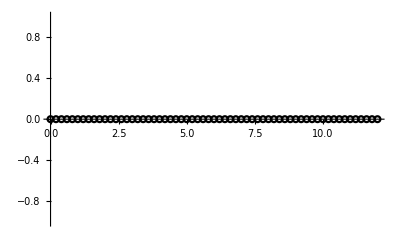

```mathematica
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/4;(*Polar Angle*)
alpha =3;
num=20;
(*NOTE: ALL THE LATTICES WILL HAVE EDGE EFFECTS*)

(*creates the linear lattice*)
list:=Table[i,{i,num}];
(*where 11 is number of particles and can be changed*)
(*i=list⟦5⟧;(*First particle of the triple*)
j=list⟦6⟧;(*Second particle of the triple*)*)





(*Define Interactions & Bloch Vector*)(*everything in terms of S, not sigma*)
(*1 is x, -1 is y, 0 is z*)
(*add d, etc. for additional spins*)
cutoff[epsilon_]:=If[Abs[epsilon] > 10^-8,epsilon,0];
hoSVD[m_]:=N[With[{d=ArrayDepth[m]},{Fold[Transpose[#1,RotateRight@Range[d]].#2&,m,#],ConjugateTranspose/@#}&@Table[Conjugate@First@SingularValueDecomposition@Flatten[m,{{i},Delete[Range[d],i]}],{i,d}]]];
J[i_,j_]:=If[Abs[i-j]==1,jstrength,0]; (*If[EuclideanDistance[i,j]==1,jstrength,0]*)(*1/Abs[j-i]^3*); (*Interaction function J depends on experimental scenario, these are two examples*)
gp[x_,θ_]:=N[Cos[θ/2]^2 ⅇ^(-ⅈ x/2)+Sin[θ/2]^2 ⅇ^(ⅈ x/2)]; 
gm[x_,θ_]:=N[Cos[θ/2]^2 ⅇ^(-ⅈ x/2)-Sin[θ/2]^2 ⅇ^(ⅈ x/2)(*+10^-20*)];(*10^-20 is to prevent 0^0 at theta = pi/2,but has to be small enough to not affect results*)

(*one correlation*)
Formula1[a_,j_,θ_,total_]:= N[(1/2)*(Sin[θ]^total)(If[total==0,Cos[θ],1])(Product[If[l==j,1,gp[a*J[j,l] t ,θ]],{l,list}])];
b[j_,θ_]:=N[{One[1,j,θ],One[-1,j,θ],One[0,j,θ]}]; (*bloch vector*)
One[a_,j_,θ_]:=(total =Abs[a];Switch[total,
0,Formula1[a,j,θ,total],
1,Sum[Formula1[x,j,θ,total]ⅇ^(-ⅈ π(x+2)(a-1)/4)/2,{x,{-1,1}}]]);

(*two correlation*)
Formula2[a_,b_,j_,k_,θ_,total_]:=N[(*(Cos[0.5J[j,k]t]-a ⅈ Cos[θ]Sin[0.5J[j,k]t ])*(Cos[0.5J[j,k]t]-b ⅈ Cos[θ] Sin[0.5J[j,k]t ])**)If[total==2,gp[a J[j,k]t,θ]*gp[b J[j,k]t,θ],1]*(*(Cos[0.5J[j,k]t]^2)**)(1/4)*(Sin[θ]^total)(If[total==0,Cos[θ]^2,1])(If[total==1,(gm[(a+b)J[j,k] t,θ]),1])(Product[If[l==j∨l==k,1,gp[a*J[j,l] t +b*J[k,l]t,θ]],{l,list}])];
Two[a_,b_,j_,k_,θ_]:= (total =Abs[a]+Abs[b];Switch[total,
0,Formula2[a,b,j,k,θ,total],
1,If[Abs[a]==1,Sum[Formula2[x,b,j,k,θ,total]ⅇ^(-ⅈ π(x+2)(a-1)/4)/2,{x,{-1,1}}],
		                 Sum[Formula2[a,y,j,k,θ,total]ⅇ^(-ⅈ π(y+2)(b-1)/4)/2,{y,{-1,1}}]],
2,Sum[Formula2[x,y,j,k,θ,total]ⅇ^(-ⅈ π((x+2)(a-1)+(y+2)(b-1))/4)/4,{x,{-1,1}},{y,{-1,1}}]]);


Connected[a_,b_,j_,k_,θ_ ]:= Two[a,b,j,k,θ]-One[a,j,θ]One[b,k,θ];
CorrTensor[j_,k_,θ_]:=Re[Table[Connected[a,b,j,k,θ], {a,{1,-1,0}},{b,{1,-1,0}}]];

ListPlot[Table[{time,(t=time;c=(Two[1,1,10,11,θ])-One[1,10,θ]One[1,11,θ];If[c<0.0001,0,c])},{time,0,12,0.2}],PlotRange->All,PlotStyle->{Black},PlotMarkers->Graphics[Circle[],ImageSize->6]]
```

# TWA

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

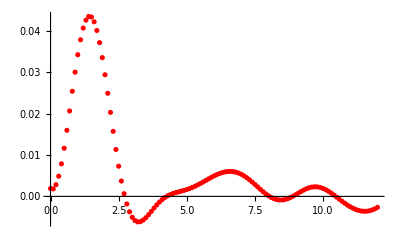

```mathematica
(*how to generalize:change polynomial by adding another xyz vector and changing the exponent in the scale factor, change  functions to accept four variables instead of three, input correct cumulant definition into connected, create Formula4[] and Four[] based on previous formulas which is easy extension, possibly change the contour value given to plot[] depending on the order of magnitude of the new correlations*)
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/4;(*Polar Angle*)
alpha =3;

samples = 5000;
num =20;

S = num/2;
Sz = S; (*removed the Dirac delta*)

individual=ProbabilityDistribution[(π*S)^(-1/2)ⅇ^(-(Spin^2)/S),{Spin,-Infinity,Infinity}];
wignershift = RotationMatrix[θ, {0,1,0}];
cdf = CDF[individual,root];
data=Table[If[condition==3,Sz/num,(root/.FindRoot[RandomReal[]==cdf,{root,1}])/Sqrt[num]],{samples},{num},{condition,3}];
cutoff[epsilon_]:=If[Abs[epsilon] > 10^-8,epsilon,0];
J[i_,j_]:=If[Abs[i-j]==1,jstrength,0];

value2[j_,k_]:=Sum[

(random = data[[x]];
(*distribution in collective spin variables with axis transform (choose a point and transform the angle with rotation operator), choose a Sperpen according to distribution, randomly choose an angle in the xy plane, cylindrical form? (Spcostheta, Spsintheta, Sz)*)
rotrandom = Table[wignershift.random[[w]],{w,num}];

(*evolve all spins through time*)
evolve = Table[
(angularv = -Sum[J[y,z]*rotrandom[[z]][[3]],{z,1,num}];
rot = angularv*t;
{rotrandom[[y]][[1]]Cos[rot] - rotrandom[[y]][[2]]Sin[rot],rotrandom[[y]][[1]]Sin[rot] + rotrandom[[y]][[2]]Cos[rot],rotrandom[[y]][[3]]}
),{y,{j,k}}];

(*measure two sites with dot product in two directions and product together, which is returned result*)
evolve[[1]][[1]]*evolve[[2]][[1]])
,{x,1,samples}]/samples;

value1[j_ ]:=Sum[

(random = data[[x]];
(*distribution in collective spin variables with axis transform (choose a point and transform the angle with rotation operator), choose a Sperpen according to distribution, randomly choose an angle in the xy plane, cylindrical form? (Spcostheta, Spsintheta, Sz)*)
rotrandom = Table[wignershift.random[[w]],{w,num}];

(*evolve all spins through time*)
evolve = Table[
(angularv = -Sum[J[y,z]*rotrandom[[z]][[3]],{z,1,num}];
rot = angularv*t;
{rotrandom[[y]][[1]]Cos[rot] - rotrandom[[y]][[2]]Sin[rot],rotrandom[[y]][[1]]Sin[rot] + rotrandom[[y]][[2]]Cos[rot],rotrandom[[y]][[3]]}
),{y,{j}}];

(*measure one site with dot product in two directions and product together, which is returned result*)
Table[evolve[[1]][[a]],{a,{1,2,3}}])

,{x,1,samples}]/samples;

ListPlot[Table[{time,(t=time;value2[10,11]-value1[10][[1]]value1[11][[1]])},{time,0,12,0.1}],PlotRange->All,PlotStyle->{Red}]
```

# TWA

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

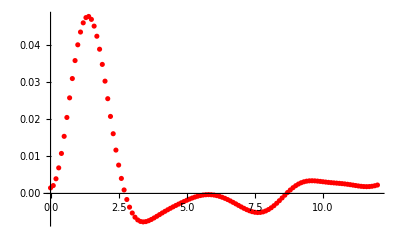

```mathematica
(*how to generalize:change polynomial by adding another xyz vector and changing the exponent in the scale factor, change  functions to accept four variables instead of three, input correct cumulant definition into connected, create Formula4[] and Four[] based on previous formulas which is easy extension, possibly change the contour value given to plot[] depending on the order of magnitude of the new correlations*)
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/4;(*Polar Angle*)
alpha =3;

samples = 10000;
num =20;

S = num/2;
Sz = S; (*removed the Dirac delta*)

individual=ProbabilityDistribution[(π*S)^(-1/2)ⅇ^(-(Spin^2)/S),{Spin,-Infinity,Infinity}];
wignershift = RotationMatrix[θ, {0,1,0}];
cdf = CDF[individual,root];
data=Table[If[condition==3,Sz/num,(root/.FindRoot[RandomReal[]==cdf,{root,1}])/Sqrt[num]],{samples},{num},{condition,3}];
cutoff[epsilon_]:=If[Abs[epsilon] > 10^-8,epsilon,0];
J[i_,j_]:=If[Abs[i-j]==1,jstrength,0];

value2[j_,k_]:=Sum[

(random = data[[x]];
(*distribution in collective spin variables with axis transform (choose a point and transform the angle with rotation operator), choose a Sperpen according to distribution, randomly choose an angle in the xy plane, cylindrical form? (Spcostheta, Spsintheta, Sz)*)
rotrandom = Table[wignershift.random[[w]],{w,num}];

(*evolve all spins through time*)
evolve = Table[
(angularv = -Sum[J[y,z]*rotrandom[[z]][[3]],{z,1,num}];
rot = angularv*t;
{rotrandom[[y]][[1]]Cos[rot] - rotrandom[[y]][[2]]Sin[rot],rotrandom[[y]][[1]]Sin[rot] + rotrandom[[y]][[2]]Cos[rot],rotrandom[[y]][[3]]}
),{y,{j,k}}];

(*measure two sites with dot product in two directions and product together, which is returned result*)
evolve[[1]][[1]]*evolve[[2]][[1]])
,{x,1,samples}]/samples;

value1[j_ ]:=Sum[

(random = data[[x]];
(*distribution in collective spin variables with axis transform (choose a point and transform the angle with rotation operator), choose a Sperpen according to distribution, randomly choose an angle in the xy plane, cylindrical form? (Spcostheta, Spsintheta, Sz)*)
rotrandom = Table[wignershift.random[[w]],{w,num}];

(*evolve all spins through time*)
evolve = Table[
(angularv = -Sum[J[y,z]*rotrandom[[z]][[3]],{z,1,num}];
rot = angularv*t;
{rotrandom[[y]][[1]]Cos[rot] - rotrandom[[y]][[2]]Sin[rot],rotrandom[[y]][[1]]Sin[rot] + rotrandom[[y]][[2]]Cos[rot],rotrandom[[y]][[3]]}
),{y,{j}}];

(*measure one site with dot product in two directions and product together, which is returned result*)
Table[evolve[[1]][[a]],{a,{1,2,3}}])

,{x,1,samples}]/samples;

ListPlot[Table[{time,(t=time;value2[10,11]-value1[10][[1]]value1[11][[1]])},{time,0,12,0.1}],PlotRange->All,PlotStyle->{Red}]
```